{KernelConfiguration[…]}

3884.66

5122.99

-Graphics-

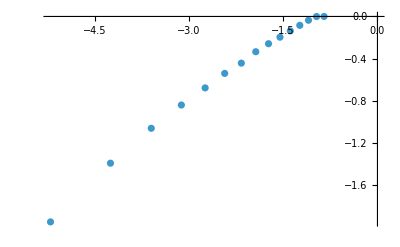

0.477942+0.441011 x

```mathematica
$DefaultParallelKernels

d=0.2;(*悬挂磁铁与吸引磁铁平面的距离*)
R=0.1;(*阻尼系数*)
g=0.2;(*重力系数*)
resolution=0.005;(*绘图分辨率*)
mypath="C:/Users/1669960040/Desktop/大物竞赛/磁力辅助/MMA导出文件";

pixels=IntegerPart[6/resolution];(*像素长度*)
unstableflag=0;(*单个像素不确定标志位*)
unstablecounts=0;(*不确定像素的个数*)
rate=0;(*不确定相空间体积分数*)
randomrange=IntegerPart[0.1*pixels];(*抽取的范围*)

mags={{-1,0},{1,0}};
f[mag_]:=(d^2+(mag[[1]]-x[t])^2+(mag[[2]]-y[t])^2)^2.5

{pictime,res}=AbsoluteTiming[ParallelTable[solution=NDSolve[{x''[t]==Plus@@Map[(#[[1]]-x[t])/f[#]&,mags]-g x[t]-R x'[t],y''[t]==Plus@@Map[(#[[2]]-y[t])/f[#]&,mags]-g y[t]-R y'[t],x[0]==i,x'[0]==0,y[0]==j,y'[0]==0},{x,y},{t,0,100},MaxSteps->200000];
final={x[100],y[100]}/. solution[[1]](*确定解的最终位置，t=100时*);
least=Map[(final-#).(final-#)&,mags](*计算最终位置和磁铁间的距离的平方*);
r=Min[least](*获取其中的最小值*);
pos=Position[least,r][[1,1]](*获取最小值的位置，即离哪个磁铁最近*);
pos-1,{j,0,3,resolution},{i,0,3,resolution}]];

pictime

(*图像拼接*)
pic1=ImageCrop[ImageReflect[ImageReflect[Graphics[Raster[res]]]],3/resolution,{-1,0}];
pic4=ImageReflect[pic1];
pic2=ColorNegate[ImageReflect[pic1,Left]];
pic3=ColorNegate[ImageReflect[pic4,Left]];
data=ImageData[Binarize[ImageCollage[{pic2,pic1,pic3,pic4}]]];


(*f-ϵ图的绘制*)
{linetime,array}=AbsoluteTiming[ParallelTable[(*分形维数计算*)For[i=1,i<=randomrange,i++,For[j=1,j<=randomrange,j++,irandom=RandomInteger[{1,pixels}];
jrandom=RandomInteger[{1,pixels}];
For[a=-ϵ^2,a<=ϵ^2,a++,If[(irandom+a)<1||(irandom+a)>pixels,Continue,(*长越界，剔除*)For[b=-ϵ^2,b<=ϵ^2,b++,If[(jrandom+b)<1||(jrandom+b)>pixels,Continue,(*宽越界，剔除*)If[data[[irandom,jrandom]]==data[[irandom+a,jrandom+b]],Continue,unstableflag++];];];];];
If[unstableflag>0,unstablecounts++,0];
unstableflag=0;];];
rate=unstablecounts/randomrange^2;
unstablecounts=0;
{Log10[((2*ϵ^2+1)/pixels)^2],Log10[rate]},{ϵ,1,Sqrt[0.2*pixels]}]];
(*array=Cases[array,{_,Except[0]}];(*去除f为1的点*)*)
(*要显示的信息*) 

linetime
Graphics[Raster[data]]
ListPlot[array]
line=Fit[array,{1,x},x]

(*文件导出*)
Export[FileNameJoin[mypath,"pics_"<>"d"<>ToString[d]<>"R"<>ToString[R]<>"g"<>ToString[g]<>".pdf"],Graphics[Raster[data]]];
Export[FileNameJoin[mypath,"pics_"<>"d"<>ToString[d]<>"R"<>ToString[R]<>"g"<>ToString[g]<>".jpg"],Graphics[Raster[data]]];
Export[FileNameJoin[mypath,"pics_"<>"d"<>ToString[d]<>"R"<>ToString[R]<>"g"<>ToString[g]<>".dat"],data];
Export[FileNameJoin[mypath,"lines_"<>"d"<>ToString[d]<>"R"<>ToString[R]<>"g"<>ToString[g]<>".dat"],array];
```